```mathematica
SetDirectory["~/Dropbox/PMB/PMBModel/Runs"];

(*vector of dispersal rates (probability of moving per day per adult)*)
dli=0.02Table[5^i,{i,-1,1,0.5}];
dli={0.02};
(*Function giving lifetime probability of dispersing, if mortality is mu and dispersal rate is p*)
pdisp[mu_,p_]:=p(1-mu)/(mu+p-mu p);
(*-------------------------------------------------------------------*)
(*corresponding vector of lifetime probability to move, if daily mortality is 0.125*)
Print[Map[pdisp[0.125,#]&,dli]];
(*-------------------------------------------------------------------*)
(*vector of fitness cots*)
xili={.8};
(*-------------------------------------------------------------------*)
(*vector of values for carrying capacity parameter*)
allis=Table[i,{i,1000,9000,2000}];
allis={5000};
```

{0.122807}

```mathematica
Do[input={"../InputData/PMBCoords.txt"}[[size]];
pa=Flatten[{numruns=1,maxT=2 365,NumPat=419,muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,bias=.9,omegaM=xili[[xx]],omegaF=xili[[xx]],drivertime=465,NumDriver=10000,NumDriverPat=1,d=dli[[dd]],L=5/111.(*5km maximum dispersal distance*),psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,allis[[a0]],al0var=0.,allis[[a1]] ,amp=0,resp=.25,recstart=365,recend=maxT,recIntGlob=1,recIntLoc=20,recsitesfreq=1,set=100000a0+10000a1+1000 size+100 rel+10 (xx)+dd,"e","r",start=0,input,"../InputData/IslandRain.csv",{"../InputData/Rellist.csv","../InputData/RellistSingle.csv"}[[rel]],outputtype=3}];
Export["Pars"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""],{rel,{2}},{size,{1}},{xx,Length[xili]},{dd,Length[dli]},{a0,Length[allis]},{a1,Length[allis]}];
```

```mathematica
out=Import["!../build/gdsimsapp<Pars"<>ToString[set]<>".csv","Table"];
MatrixForm[out[[64;;117]]];
```

```mathematica
dat=Import["../InputData/Rel2Vil.txt","Table"];
Dimensions[dat]
```

{726,6}

```mathematica
dat[[1;;5]]
datB=dat[[All,1;;4]];
Dimensions[datB]
Export["../InputData/Rel2VilB.txt",datB,"Table"];
```

{{32.5845,-0.0867053,0.0413223,5,1,1},{32.5854,-0.0858003,0.289256,5,1,1},{32.5854,-0.0867053,0.801653,5,1,1},{32.5854,-0.0876102,0.0578512,5,1,1},{32.5863,0.0345617,0.0495868,1,1,1}}

{726,4}

```mathematica
out[[50]]
```

{inherit,2,1,1,0}

{635,7}

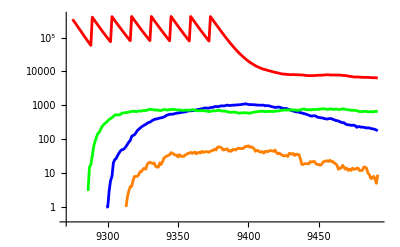

```mathematica
tot=Drop[Import["./output_files/Totals"<>ToString[set]<>"run1.txt","Table"],100];
Dimensions[tot]
ListLogPlot[Table[tot[[All,{1,ii}]],{ii,{3,4,6,7}}],PlotRange->All,Joined->True,PlotStyle->{Red,Blue,Green,Orange}]
```

```mathematica
set
```

111121

```mathematica
out[[1;;10]]
```

{}